```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

URLFetch::invhttp: Couldn't connect to server.

{KernelObject(1,local),KernelObject(2,local),KernelObject(3,local),KernelObject(4,local),KernelObject(5,local),KernelObject(6,local),KernelObject(7,local),KernelObject(8,local)}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

The amplitude

```mathematica
MVG[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=If[ω2>ω1,4 g^2 ω1 NIntegrate[1/(1+y ω1-x+ω2-ω1)^2 ϕ1[x/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[1+((y-1)ω1)/ω2],{x,0,1},{y,0,1}],4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(1+y ω2-x(ω1-ω2-1))^2 ϕ1[x]ϕ2[1+(y-1)ω2/ω1]ϕ3[x(1+ω2-ω1)]ϕ4[y],{x,0,1},{y,0,1}]]
```

```mathematica
MHG[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=If[ω2>ω1,4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}],4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(y ω2-x(1+ω2-ω1)-ω1)^2 ϕ1[x]ϕ2[(y ω2)/ω1]ϕ3[ω1-ω2+(1-ω1+ω2)x]ϕ4[y],{x,0,1},{y,0,1}]]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;g=1;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
ωfp[z_][M1_,M2_,M3_,M4_]:=(-√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 1.*)
```

```mathematica
ωfn[z_][M1_,M2_,M3_,M4_]:=(√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 2*)
```

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
ω2n[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1);(*transform ω1 to ω2, your definition, solution 2*)
```

```mathematica
Sz[z_][M1_,M2_]:=M1^2/(1-z)+M2^2/z;(*Centre of mass energy*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
zfω1[ω1_][MA_,MB_,MC_,MD_]:=ω1/(1+ω2n[ω1][MA,MB,MC,MD])(*transform ω1 to z, using z=ω1/(1+ω2) and previous result of ω1 to ω2*)
ωfω1[ω1_][MA_,MB_,MC_,MD_]:=(ω2n[ω1][MA,MB,MC,MD])/(1+ω2n[ω1][MA,MB,MC,MD]);
```

```mathematica
ω1fz[z_][M1_,M2_,M3_,M4_]:=-z/(ωfp[z][M1,M2,M3,M4]-1);
ω2fz[z_][M1_,M2_,M3_,M4_]:=(-ωfp[z][M1,M2,M3,M4])/(ωfp[z][M1,M2,M3,M4]-1);(*transform z to ω1 and ω2, using z=ω1/(1+ω2) and previous result of z to ω*)
```

```mathematica
MVGab[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω,ΦBbar},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Set@@{ΦBbar[x_],-ΦB[1-x]};
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[0];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MVG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.1,0.3,0.1}]~Join~ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MVG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.3,0.9,0.005}]~Join~
ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MVG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.9,0.999,0.003}]
]
```

```mathematica
MHGab[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω,ΦBbar},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Set@@{ΦBbar[x_],-ΦB[1-x]};
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[0];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MHG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.1,0.3,0.1}]~Join~ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MHG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.3,0.999,0.003}]
]
```

```mathematica
Msum[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,ΦBbar,Sen},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Set@@{ΦBbar[x_],-ΦB[1-x]};
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[0];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,
(*Print["ω1=",ω1,"    ω2=",ω2];*)(*it's for debug purpose, you can comment this*){Sen,MVG[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+MHG[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]],{ω1,0.003,ω/.FindMinimum[Sω1[ω][M1,M2,M3,M4],{ω,0.5}][[2]],0.01}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

Two amplitudes separately (note that the horizontal axis is ω1, so it must be transformed into S using function Sω1[ω1][M1,M2,M3,M4]), one convenient way is to use the last line in this section, just don’t do the sum up):

```mathematica
MVGva=MVGab[80,60,1]
```

Wavefunction build complete.

M1=141.057  M2=141.057  M3=140.322  M4=140.322

z=0.1    ω=0.0988464

z=0.2    ω=0.197408

z=0.3    ω=0.295565

z=0.3    ω=0.295565

z=0.33    ω=0.324906

z=0.355    ω=0.349312

z=0.38    ω=0.373669

z=0.405    ω=0.397974

z=0.43    ω=0.422219

z=0.455    ω=0.446397

z=0.48    ω=0.470496

z=0.485    ω=0.475306

z=0.46    ω=0.451223

z=0.435    ω=0.427061

z=0.41    ω=0.402828

z=0.36    ω=0.354187

z=0.335    ω=0.329791

z=0.305    ω=0.300459

z=0.385    ω=0.378535

z=0.49    ω=0.480112

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.465    ω=0.456046

z=0.44    ω=0.431899

z=0.415    ω=0.40768

z=0.39    ω=0.383398

z=0.365    ω=0.359061

z=0.495    ω=0.484914

z=0.34    ω=0.334674

z=0.47    ω=0.460866

z=0.31    ω=0.305352

z=0.445    ω=0.436735

z=0.42    ω=0.412529

z=0.5    ω=0.489712

z=0.395    ω=0.388259

z=0.475    ω=0.465683

z=0.37    ω=0.363932

z=0.345    ω=0.339555

z=0.45    ω=0.441567

z=0.505    ω=0.494507

z=0.315    ω=0.310243

z=0.425    ω=0.417376

z=0.53    ω=0.518414

z=0.4    ω=0.393118

z=0.51    ω=0.499297

z=0.555    ω=0.542202

z=0.375    ω=0.368802

z=0.535    ω=0.523182

z=0.35    ω=0.344434

z=0.58    ω=0.565849

z=0.32    ω=0.315132

z=0.56    ω=0.546943

z=0.515    ω=0.504083

z=0.54    ω=0.527945

z=0.605    ω=0.589329

z=0.585    ω=0.570559

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.565    ω=0.551679

z=0.63    ω=0.612609

z=0.52    ω=0.508865

z=0.61    ω=0.594002

z=0.545    ω=0.532702

z=0.655    ω=0.635647

z=0.59    ω=0.575262

z=0.635    ω=0.617238

z=0.57    ω=0.556408

z=0.325    ω=0.32002

z=0.615    ω=0.598667

z=0.66    ω=0.640221

z=0.525    ω=0.513642

z=0.595    ω=0.579959

z=0.64    ω=0.621856

z=0.55    ω=0.537455

z=0.665    ω=0.644783

z=0.575    ω=0.561132

z=0.62    ω=0.603323

z=0.645    ω=0.626464

z=0.6    ω=0.584648

z=0.68    ω=0.658389

z=0.67    ω=0.649332

z=0.705    ω=0.680761

z=0.625    ω=0.607971

z=0.73    ω=0.702664

z=0.65    ω=0.631061

z=0.685    ω=0.662896

z=0.675    ω=0.653868

z=0.71    ω=0.685183

z=0.755    ω=0.723962

z=0.78    ω=0.744456

z=0.735    ω=0.706978

z=0.805    ω=0.763855

z=0.76    ω=0.728133

z=0.83    ω=0.781701

z=0.69    ω=0.667387

z=0.785    ω=0.748435

z=0.715    ω=0.689585

z=0.855    ω=0.797248

z=0.74    ω=0.711266

z=0.81    ω=0.767567

z=0.835    ω=0.785026

z=0.765    ω=0.73227

z=0.86    ω=0.79998

z=0.79    ω=0.752368

z=0.84    ω=0.788252

z=0.815    ω=0.771213

z=0.72    ω=0.693967

z=0.865    ω=0.802557

z=0.695    ω=0.671862

z=0.745    ω=0.715527

z=0.77    ω=0.736371

z=0.795    ω=0.756251

z=0.845    ω=0.791372

z=0.82    ω=0.774788

z=0.87    ω=0.804961

z=0.875    ω=0.807173

z=0.85    ω=0.794374

z=0.75    ω=0.719759

z=0.8    ω=0.760081

z=0.825    ω=0.778286

z=0.775    ω=0.740434

z=0.725    ω=0.698327

z=0.7    ω=0.67632

z=0.88    ω=0.809172

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.885    ω=0.810932

z=0.89    ω=0.812423

z=0.895    ω=0.81361

z=0.9    ω=0.814452

z=0.9    ω=0.814452

z=0.909    ω=0.814935

z=0.918    ω=0.813762

z=0.924    ω=0.811803

z=0.93    ω=0.808658

z=0.936    ω=0.80404

z=0.942    ω=0.797562

z=0.948    ω=0.788689

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.933    ω=0.806555

z=0.951    ω=0.783127

z=0.939    ω=0.801063

z=0.945    ω=0.793466

z=0.927    ω=0.810395

z=0.921    ω=0.812916

z=0.903    ω=0.814772

z=0.912    ω=0.814751

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.954    ω=0.776656

z=0.96    ω=0.76034

z=0.966    ω=0.738005

z=0.972    ω=0.70684

z=0.978    ω=0.661954

z=0.984    ω=0.594029

z=0.915    ω=0.814366

z=0.906    ω=0.814937

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.957    ω=0.769124

z=0.963    ω=0.750067

z=0.969    ω=0.723766

z=0.975    ω=0.686547

z=0.99    ω=0.482839

z=0.996    ω=0.274688

z=0.981    ω=0.63175

z=0.987    ω=0.545913

z=0.993    ω=0.397115

z=0.999    ω=0.0868413

(0.1 | 2.23772×10^-6
0.2 | 0.0000121274
0.3 | 0.0000492934
0.3 | 0.0000492934
0.305 | 0.0000526729
0.31 | 0.0000562701
0.315 | 0.0000600985
0.32 | 0.000064173
0.325 | 0.000068509
0.33 | 0.0000731232
0.335 | 0.0000780332
0.34 | 0.0000832581
0.345 | 0.0000888178
0.35 | 0.0000947339
0.355 | 0.000101029
0.36 | 0.000107728
0.365 | 0.000114857
0.37 | 0.000122443
0.375 | 0.000130516
0.38 | 0.000139108
0.385 | 0.000148254
0.39 | 0.000157988
0.395 | 0.00016835
0.4 | 0.000179381
0.405 | 0.000191125
0.41 | 0.000203631
0.415 | 0.000216947
0.42 | 0.00023113
0.425 | 0.000246237
0.43 | 0.00026233
0.435 | 0.000279477
0.44 | 0.000297748
0.445 | 0.00031722
0.45 | 0.000337977
0.455 | 0.000360106
0.46 | 0.000383703
0.465 | 0.000408869
0.47 | 0.000435714
0.475 | 0.000464356
0.48 | 0.000494922
0.485 | 0.000527548
0.49 | 0.000562381
0.495 | 0.000599579
0.5 | 0.000639312
0.505 | 0.000681764
0.51 | 0.000727132
0.515 | 0.000775631
0.52 | 0.000827489
0.525 | 0.000882957
0.53 | 0.000942303
0.535 | 0.00100582
0.54 | 0.00107381
0.545 | 0.00114663
0.55 | 0.00122463
0.555 | 0.00130823
0.56 | 0.00139783
0.565 | 0.00149393
0.57 | 0.00159702
0.575 | 0.00170764
0.58 | 0.00182641
0.585 | 0.00195396
0.59 | 0.00209101
0.595 | 0.00223831
0.6 | 0.0023967
0.605 | 0.00256709
0.61 | 0.00275047
0.615 | 0.0029479
0.62 | 0.00316058
0.625 | 0.00338977
0.63 | 0.00363687
0.635 | 0.00390341
0.64 | 0.00419106
0.645 | 0.00450163
0.65 | 0.00483713
0.655 | 0.00519972
0.66 | 0.0055918
0.665 | 0.00601599
0.67 | 0.00647513
0.675 | 0.00697238
0.68 | 0.00751116
0.685 | 0.00809527
0.69 | 0.00872882
0.695 | 0.00941638
0.7 | 0.0101629
0.705 | 0.0109739
0.71 | 0.0118554
0.715 | 0.0128138
0.72 | 0.0138566
0.725 | 0.0149916
0.73 | 0.0162275
0.735 | 0.0175738
0.74 | 0.0190409
0.745 | 0.0206403
0.75 | 0.0223844
0.755 | 0.0242866
0.76 | 0.0263618
0.765 | 0.0286259
0.77 | 0.0310961
0.775 | 0.0337909
0.78 | 0.0367301
0.785 | 0.0399348
0.79 | 0.043427
0.795 | 0.0472239
0.8 | 0.0513663
0.805 | 0.0558604
0.81 | 0.060735
0.815 | 0.0660115
0.82 | 0.0717083
0.825 | 0.0778394
0.83 | 0.084412
0.835 | 0.0914232
0.84 | 0.0988573
0.845 | 0.10668
0.85 | 0.114833
0.855 | 0.123227
0.86 | 0.131736
0.865 | 0.140181
0.87 | 0.148329
0.875 | 0.155878
0.88 | 0.16245
0.885 | 0.167587
0.89 | 0.170718
0.895 | 0.171376
0.9 | 0.168838
0.9 | 0.168838
0.903 | 0.165566
0.906 | 0.16086
0.909 | 0.154653
0.912 | 0.146918
0.915 | 0.137682
0.918 | 0.12704
0.921 | 0.115159
0.924 | 0.102294
0.927 | 0.088777
0.93 | 0.0750184
0.933 | 0.0614794
0.936 | 0.0486404
0.939 | 0.0369507
0.942 | 0.0268033
0.945 | 0.0184316
0.948 | 0.0119276
0.951 | 0.00720543
0.954 | 0.00402984
0.957 | 0.00207037
0.96 | 0.000970967
0.963 | 0.000414285
0.966 | 0.000160994
0.969 | 0.0000573415
0.972 | 0.0000189106
0.975 | 5.8314×10^-6
0.978 | 1.68645×10^-6
0.981 | 4.52932×10^-7
0.984 | 1.10407×10^-7
0.987 | 2.36321×10^-8
0.99 | 4.3707×10^-9
0.993 | 6.15263×10^-10
0.996 | 3.96424×10^-11
0.999 | 9.93905×10^-14)

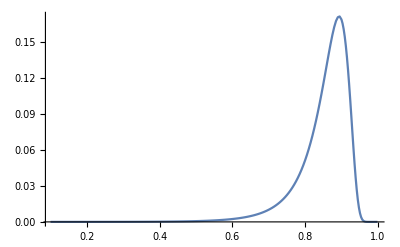

```mathematica
ListPlot[Re[MVGva],PlotRange->All,Joined->True]
ListPlot[Table[{Sω1[x][Msumdat[[1,1]],Msumdat[[1,2]],Msumdat[[1,3]],Msumdat[[1,4]]],Interpolation[MVGva][x]},{x,0.8,0.9,0.001}]]
```

```mathematica
MHGva=MHGab[80,60,1]
```

Wavefunction build complete.

M1=141.057  M2=141.057  M3=140.322  M4=140.322

z=0.1    ω=0.0988464

z=0.2    ω=0.197408

z=0.3    ω=0.295565

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.3    ω=0.295565

z=0.33    ω=0.324906

z=0.36    ω=0.354187

z=0.39    ω=0.383398

z=0.42    ω=0.412529

z=0.45    ω=0.441567

z=0.48    ω=0.470496

z=0.51    ω=0.499297

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.513    ω=0.502169

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.483    ω=0.473382

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.453    ω=0.444465

z=0.423    ω=0.415437

z=0.393    ω=0.386315

z=0.363    ω=0.357111

z=0.333    ω=0.327837

z=0.303    ω=0.298502

z=0.516    ω=0.50504

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.486    ω=0.476267

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.456    ω=0.447362

z=0.426    ω=0.418345

z=0.396    ω=0.389231

z=0.519    ω=0.507909

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.366    ω=0.360035

z=0.336    ω=0.330768

z=0.489    ω=0.479151

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.306    ω=0.301438

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.459    ω=0.450258

z=0.399    ω=0.392146

z=0.522    ω=0.510776

z=0.429    ω=0.421251

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.492    ω=0.482033

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.369    ω=0.362958

z=0.339    ω=0.333697

z=0.462    ω=0.453153

z=0.525    ω=0.513642

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.309    ω=0.304373

z=0.402    ω=0.395061

z=0.432    ω=0.424156

z=0.495    ω=0.484914

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.528    ω=0.516506

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.465    ω=0.456046

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.372    ω=0.36588

z=0.498    ω=0.487794

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.531    ω=0.519368

z=0.342    ω=0.336626

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.435    ω=0.427061

z=0.405    ω=0.397974

z=0.312    ω=0.307308

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.468    ω=0.458939

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.534    ω=0.522229

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.501    ω=0.490672

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.438    ω=0.429964

z=0.375    ω=0.368802

z=0.408    ω=0.400887

z=0.345    ω=0.339555

z=0.471    ω=0.46183

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.537    ω=0.525088

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.315    ω=0.310243

z=0.504    ω=0.493548

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.441    ω=0.432866

z=0.54    ω=0.527945

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.474    ω=0.46472

z=0.378    ω=0.371723

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.507    ω=0.496423

z=0.411    ω=0.403799

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.348    ω=0.342483

z=0.543    ω=0.5308

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.318    ω=0.313177

z=0.444    ω=0.435768

z=0.477    ω=0.467609

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.57    ω=0.556408

z=0.381    ω=0.374643

z=0.414    ω=0.40671

z=0.546    ω=0.533653

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.351    ω=0.34541

z=0.573    ω=0.559243

z=0.447    ω=0.438668

z=0.6    ω=0.584648

z=0.321    ω=0.31611

z=0.549    ω=0.536505

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.576    ω=0.562076

z=0.603    ω=0.587457

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.417    ω=0.40962

z=0.384    ω=0.377562

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.354    ω=0.348336

z=0.552    ω=0.539354

z=0.63    ω=0.612609

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.579    ω=0.564906

z=0.606    ω=0.590264

z=0.633    ω=0.615387

z=0.555    ω=0.542202

z=0.324    ω=0.319043

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.609    ω=0.593068

z=0.66    ω=0.640221

z=0.582    ω=0.567734

z=0.387    ω=0.38048

z=0.636    ω=0.618162

z=0.357    ω=0.351262

z=0.663    ω=0.64296

z=0.558    ω=0.545047

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.612    ω=0.595869

z=0.585    ω=0.570559

z=0.639    ω=0.620933

z=0.666    ω=0.645694

z=0.615    ω=0.598667

z=0.561    ω=0.547891

z=0.327    ω=0.321975

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.642    ω=0.623701

z=0.588    ω=0.573382

z=0.669    ω=0.648423

z=0.69    ω=0.667387

z=0.618    ω=0.601462

z=0.72    ω=0.693967

z=0.645    ω=0.626464

z=0.693    ω=0.670074

z=0.672    ω=0.651148

z=0.564    ω=0.550732

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.591    ω=0.576202

z=0.723    ω=0.696586

z=0.648    ω=0.629224

z=0.696    ω=0.672755

z=0.621    ω=0.604253

z=0.675    ω=0.653868

z=0.726    ω=0.699196

z=0.567    ω=0.553571

z=0.594    ω=0.57902

z=0.75    ω=0.719759

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.699    ω=0.67543

z=0.651    ω=0.63198

z=0.678    ω=0.656582

z=0.729    ω=0.701799

z=0.624    ω=0.607042

z=0.753    ω=0.722285

z=0.702    ω=0.678099

z=0.732    ω=0.704393

z=0.681    ω=0.659291

z=0.78    ω=0.744456

z=0.654    ω=0.634731

z=0.597    ω=0.581835

z=0.756    ω=0.724799

z=0.627    ω=0.609827

z=0.783    ω=0.746849

z=0.735    ω=0.706978

z=0.705    ω=0.680761

z=0.759    ω=0.727301

z=0.684    ω=0.661995

z=0.657    ω=0.637478

z=0.786    ω=0.749226

z=0.738    ω=0.709554

z=0.81    ω=0.767567

z=0.762    ω=0.729792

z=0.708    ω=0.683416

z=0.84    ω=0.788252

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.789    ω=0.751585

z=0.687    ω=0.664694

z=0.813    ω=0.769763

z=0.843    ω=0.790138

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.765    ω=0.73227

z=0.741    ω=0.71212

z=0.867    ω=0.80354

z=0.792    ω=0.753928

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.711    ω=0.686065

z=0.816    ω=0.771934

z=0.846    ω=0.791982

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.87    ω=0.804961

z=0.849    ω=0.793783

z=0.768    ω=0.734735

z=0.894    ω=0.813399

z=0.819    ω=0.774079

z=0.795    ω=0.756251

z=0.873    ω=0.806313

z=0.744    ω=0.714677

z=0.897    ω=0.813991

z=0.852    ω=0.79554

z=0.876    ω=0.807591

z=0.714    ω=0.688706

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.822    ω=0.776197

z=0.9    ω=0.814452

z=0.798    ω=0.758556

z=0.879    ω=0.808791

z=0.855    ω=0.797248

z=0.771    ω=0.737187

z=0.903    ω=0.814772

z=0.747    ω=0.717223

z=0.825    ω=0.778286

z=0.882    ω=0.809906

z=0.858    ω=0.798905

z=0.906    ω=0.814937

z=0.801    ω=0.760841

z=0.717    ω=0.69134

z=0.885    ω=0.810932

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.774    ω=0.739625

z=0.909    ω=0.814935

z=0.861    ω=0.800508

z=0.828    ω=0.780346

z=0.888    ω=0.811861

z=0.912    ω=0.814751

z=0.804    ω=0.763105

z=0.921    ω=0.812916

z=0.864    ω=0.802055

z=0.831    ω=0.782374

z=0.891    ω=0.812686

z=0.915    ω=0.814366

z=0.924    ω=0.811803

z=0.777    ω=0.742048

z=0.948    ω=0.788689

z=0.975    ω=0.686547

z=0.918    ω=0.813762

z=0.927    ω=0.810395

z=0.807    ω=0.765347

z=0.951    ω=0.783127

z=0.978    ω=0.661954

z=0.834    ω=0.784369

z=0.93    ω=0.808658

z=0.954    ω=0.776656

z=0.981    ω=0.63175

z=0.957    ω=0.769124

z=0.933    ω=0.806555

z=0.837    ω=0.786329

z=0.96    ω=0.76034

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.936    ω=0.80404

z=0.984    ω=0.594029

z=0.963    ω=0.750067

z=0.939    ω=0.801063

z=0.966    ω=0.738005

z=0.987    ω=0.545913

z=0.942    ω=0.797562

z=0.969    ω=0.723766

z=0.945    ω=0.793466

z=0.99    ω=0.482839

z=0.972    ω=0.70684

z=0.993    ω=0.397115

z=0.996    ω=0.274688

z=0.999    ω=0.0868413

(0.1 | 0.0000299283
0.2 | 0.0000795714
0.3 | 0.000196759
0.3 | 0.000196759
0.303 | 0.000202244
0.306 | 0.000207889
0.309 | 0.000213699
0.312 | 0.000219679
0.315 | 0.000225836
0.318 | 0.000232174
0.321 | 0.0002387
0.324 | 0.000245419
0.327 | 0.000252337
0.33 | 0.000259462
0.333 | 0.0002668
0.336 | 0.000274357
0.339 | 0.000282142
0.342 | 0.00029016
0.345 | 0.000298421
0.348 | 0.000306931
0.351 | 0.0003157
0.354 | 0.000324735
0.357 | 0.000334046
0.36 | 0.000343642
0.363 | 0.000353531
0.366 | 0.000363725
0.369 | 0.000374234
0.372 | 0.000385067
0.375 | 0.000396236
0.378 | 0.000407752
0.381 | 0.000419627
0.384 | 0.000431873
0.387 | 0.000444504
0.39 | 0.000457532
0.393 | 0.00047097
0.396 | 0.000484834
0.399 | 0.000499138
0.402 | 0.000513897
0.405 | 0.000529127
0.408 | 0.000544845
0.411 | 0.000561067
0.414 | 0.000577813
0.417 | 0.000595099
0.42 | 0.000612946
0.423 | 0.000631374
0.426 | 0.000650403
0.429 | 0.000670055
0.432 | 0.000690353
0.435 | 0.000711319
0.438 | 0.000732979
0.441 | 0.000755358
0.444 | 0.000778482
0.447 | 0.000802378
0.45 | 0.000827075
0.453 | 0.000852604
0.456 | 0.000878994
0.459 | 0.000906278
0.462 | 0.000934491
0.465 | 0.000963666
0.468 | 0.00099384
0.471 | 0.00102505
0.474 | 0.00105734
0.477 | 0.00109075
0.48 | 0.00112532
0.483 | 0.00116109
0.486 | 0.00119812
0.489 | 0.00123645
0.492 | 0.00127614
0.495 | 0.00131723
0.498 | 0.00135979
0.501 | 0.00140386
0.504 | 0.00144952
0.507 | 0.00149682
0.51 | 0.00154583
0.513 | 0.00159663
0.516 | 0.00164927
0.519 | 0.00170385
0.522 | 0.00176043
0.525 | 0.00181911
0.528 | 0.00187996
0.531 | 0.00194308
0.534 | 0.00200857
0.537 | 0.00207651
0.54 | 0.00214703
0.543 | 0.00222021
0.546 | 0.00229619
0.549 | 0.00237508
0.552 | 0.00245701
0.555 | 0.0025421
0.558 | 0.00263049
0.561 | 0.00272233
0.564 | 0.00281778
0.567 | 0.00291698
0.57 | 0.00302012
0.573 | 0.00312735
0.576 | 0.00323887
0.579 | 0.00335487
0.582 | 0.00347556
0.585 | 0.00360114
0.588 | 0.00373185
0.591 | 0.00386791
0.594 | 0.00400958
0.597 | 0.00415712
0.6 | 0.00431081
0.603 | 0.00447093
0.606 | 0.00463779
0.609 | 0.00481171
0.612 | 0.00499303
0.615 | 0.0051821
0.618 | 0.00537931
0.621 | 0.00558505
0.624 | 0.00579974
0.627 | 0.00602381
0.63 | 0.00625775
0.633 | 0.00650203
0.636 | 0.00675718
0.639 | 0.00702374
0.642 | 0.00730231
0.645 | 0.00759348
0.648 | 0.00789792
0.651 | 0.0082163
0.654 | 0.00854935
0.657 | 0.00889785
0.66 | 0.0092626
0.663 | 0.00964448
0.666 | 0.0100444
0.669 | 0.0104633
0.672 | 0.0109022
0.675 | 0.0113623
0.678 | 0.0118446
0.681 | 0.0123504
0.684 | 0.012881
0.687 | 0.0134378
0.69 | 0.0140222
0.693 | 0.0146358
0.696 | 0.0152804
0.699 | 0.0159575
0.702 | 0.0166692
0.705 | 0.0174173
0.708 | 0.0182041
0.711 | 0.0190318
0.714 | 0.0199028
0.717 | 0.0208197
0.72 | 0.0217852
0.723 | 0.0228023
0.726 | 0.023874
0.729 | 0.0250037
0.732 | 0.026195
0.735 | 0.0274515
0.738 | 0.0287775
0.741 | 0.0301771
0.744 | 0.0316551
0.747 | 0.0332163
0.75 | 0.034866
0.753 | 0.0366099
0.756 | 0.038454
0.759 | 0.0404047
0.762 | 0.0424691
0.765 | 0.0446543
0.768 | 0.0469684
0.771 | 0.0494198
0.774 | 0.0520176
0.777 | 0.0547713
0.78 | 0.0576915
0.783 | 0.0607891
0.786 | 0.0640761
0.789 | 0.067565
0.792 | 0.0712695
0.795 | 0.0752039
0.798 | 0.0793838
0.801 | 0.0838255
0.804 | 0.0885467
0.807 | 0.093566
0.81 | 0.0989034
0.813 | 0.10458
0.816 | 0.110618
0.819 | 0.117041
0.822 | 0.123874
0.825 | 0.131144
0.828 | 0.138878
0.831 | 0.147105
0.834 | 0.155854
0.837 | 0.165156
0.84 | 0.175044
0.843 | 0.185549
0.846 | 0.196704
0.849 | 0.20854
0.852 | 0.221089
0.855 | 0.234379
0.858 | 0.248436
0.861 | 0.263283
0.864 | 0.278937
0.867 | 0.295406
0.87 | 0.31269
0.873 | 0.330775
0.876 | 0.349631
0.879 | 0.36921
0.882 | 0.389436
0.885 | 0.410204
0.888 | 0.431374
0.891 | 0.452759
0.894 | 0.474123
0.897 | 0.495167
0.9 | 0.515525
0.903 | 0.534752
0.906 | 0.552317
0.909 | 0.567601
0.912 | 0.579891
0.915 | 0.588388
0.918 | 0.592221
0.921 | 0.590479
0.924 | 0.582249
0.927 | 0.56669
0.93 | 0.543124
0.933 | 0.511154
0.936 | 0.470802
0.939 | 0.42266
0.942 | 0.36802
0.945 | 0.308949
0.948 | 0.248244
0.951 | 0.189241
0.954 | 0.135411
0.957 | 0.0897856
0.96 | 0.0543315
0.963 | 0.0294809
0.966 | 0.0140694
0.969 | 0.00579218
0.972 | 0.0020246
0.975 | 0.000596573
0.978 | 0.000149125
0.981 | 0.000032164
0.984 | 6.04637×10^-6
0.987 | 9.65031×10^-7
0.99 | 1.18859×10^-7
0.993 | 9.57987×10^-9
0.996 | 4.18683×10^-10
0.999 | 6.90336×10^-13)

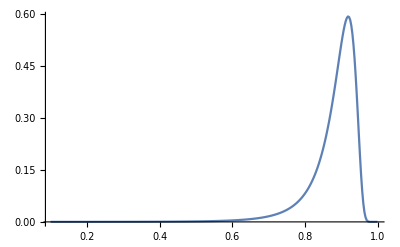

```mathematica
ListPlot[Re[MHGva],PlotRange->All,Joined->True]
```

```mathematica
ListPlot[Table[{Sω1[x],Interpolation[MVGva][x]+Interpolation[MHGva][x]},{x,0,1}]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Interpolation::inddp: The point 0.3 in dimension 1 is duplicated.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

Interpolation::inddp: The point 0.3 in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

-Graphics-

The total amplitude (and the square):

```mathematica
Msumdat=Msum[80,60]
```

Wavefunction build complete.

M1=141.057  M2=141.057  M3=140.322  M4=140.322

ω1=0.003    ω2=0.00296872

ω1=0.063    ω2=0.0623016

ω1=0.123    ω2=0.121544

ω1=0.183    ω2=0.180677

ω1=0.243    ω2=0.239674

ω1=0.303    ω2=0.298502

ω1=0.363    ω2=0.357111

ω1=0.423    ω2=0.415437

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.433    ω2=0.425125

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.373    ω2=0.366854

ω1=0.313    ω2=0.308287

ω1=0.253    ω2=0.249492

ω1=0.193    ω2=0.19052

ω1=0.133    ω2=0.131408

ω1=0.073    ω2=0.0721821

ω1=0.443    ω2=0.434801

ω1=0.013    ω2=0.0128631

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.383    ω2=0.376589

ω1=0.323    ω2=0.318065

ω1=0.453    ω2=0.444465

ω1=0.263    ω2=0.259304

ω1=0.203    ω2=0.200359

ω1=0.143    ω2=0.141269

ω1=0.393    ω2=0.386315

ω1=0.083    ω2=0.08206

ω1=0.463    ω2=0.454117

ω1=0.333    ω2=0.327837

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.023    ω2=0.0227554

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.273    ω2=0.269112

ω1=0.403    ω2=0.396032

ω1=0.473    ω2=0.463757

ω1=0.213    ω2=0.210195

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.153    ω2=0.151126

ω1=0.343    ω2=0.337603

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.483    ω2=0.473382

ω1=0.413    ω2=0.40574

ω1=0.093    ω2=0.0919353

ω1=0.283    ω2=0.278914

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.223    ω2=0.220026

ω1=0.493    ω2=0.482994

ω1=0.033    ω2=0.0326454

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.353    ω2=0.347361

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.543    ω2=0.5308

ω1=0.163    ω2=0.16098

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.503    ω2=0.492589

ω1=0.293    ω2=0.288711

ω1=0.553    ω2=0.540304

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.103    ω2=0.101808

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.233    ω2=0.229852

ω1=0.603    ω2=0.587457

ω1=0.513    ω2=0.502169

ω1=0.563    ω2=0.549785

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.613    ω2=0.596802

ω1=0.173    ω2=0.17083

ω1=0.573    ω2=0.559243

ω1=0.043    ω2=0.0425332

ω1=0.523    ω2=0.511731

ω1=0.663    ω2=0.64296

ω1=0.623    ω2=0.606113

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.673    ω2=0.652055

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.583    ω2=0.568676

ω1=0.713    ω2=0.687827

ω1=0.533    ω2=0.521275

ω1=0.633    ω2=0.615387

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.113    ω2=0.111678

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.683    ω2=0.661095

ω1=0.723    ω2=0.696586

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.643    ω2=0.624622

ω1=0.593    ω2=0.578081

ω1=0.733    ω2=0.705255

ω1=0.693    ω2=0.670074

ω1=0.763    ω2=0.730619

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.813    ω2=0.769763

ω1=0.653    ω2=0.633814

ω1=0.743    ω2=0.713826

ω1=0.703    ω2=0.678987

ω1=0.773    ω2=0.738814

ω1=0.823    ω2=0.776896

ω1=0.863    ω2=0.801546

ω1=0.873    ω2=0.806313

ω1=0.833    ω2=0.783707

ω1=0.753    ω2=0.722285

ω1=0.783    ω2=0.746849

ω1=0.883    ω2=0.810259

ω1=0.843    ω2=0.790138

ω1=0.893    ω2=0.813174

ω1=0.053    ω2=0.0524186

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω1=0.793    ω2=0.754704

ω1=0.853    ω2=0.796114

ω1=0.903    ω2=0.814772

ω1=0.803    ω2=0.762352

{{141.057,141.057,140.322,140.322},(2583.02 | 9.43276×10^-7
1253.15 | 4.02867×10^-6
951.384 | 7.05282×10^-6
801.985 | 0.0000100526
709.336 | 0.0000130637
645.018 | 0.0000161213
597.206 | 0.00001926
559.989 | 0.000022515
530.043 | 0.0000259217
505.337 | 0.0000295169
484.553 | 0.0000333387
466.79 | 0.0000374273
451.414 | 0.0000418249
437.96 | 0.0000465772
426.08 | 0.0000517327
415.508 | 0.0000573443
406.036 | 0.0000634692
397.5 | 0.0000701701
389.767 | 0.0000775155
382.73 | 0.0000855807
376.298 | 0.0000944488
370.399 | 0.000104212
364.971 | 0.000114971
359.96 | 0.000126839
355.322 | 0.000139942
351.019 | 0.000154418
347.018 | 0.000170424
343.289 | 0.000188133
339.807 | 0.00020774
336.55 | 0.000229461
333.499 | 0.00025354
330.637 | 0.00028025
327.948 | 0.000309899
325.418 | 0.000342832
323.035 | 0.000379439
320.789 | 0.000420157
318.669 | 0.000465483
316.666 | 0.000515978
314.772 | 0.000572276
312.98 | 0.000635097
311.283 | 0.000705259
309.676 | 0.000783692
308.151 | 0.000871454
306.705 | 0.000969753
305.332 | 0.00107997
304.028 | 0.00120369
302.79 | 0.00134271
301.613 | 0.00149913
300.494 | 0.00167533
299.429 | 0.00187408
298.417 | 0.00209856
297.454 | 0.00235247
296.537 | 0.00264008
295.665 | 0.00296636
294.835 | 0.00333711
294.045 | 0.0037591
293.292 | 0.00424024
292.576 | 0.0047898
291.895 | 0.00541871
291.246 | 0.00613983
290.629 | 0.00696836
290.043 | 0.00792234
289.484 | 0.00902318
288.954 | 0.0102964
288.449 | 0.0117725
287.97 | 0.0134879
287.515 | 0.0154868
287.083 | 0.0178218
286.674 | 0.0205572
286.286 | 0.0237704
285.919 | 0.0275558
285.571 | 0.0320283
285.243 | 0.0373283
284.933 | 0.0436277
284.64 | 0.0511373
284.365 | 0.0601157
284.107 | 0.0708801
283.865 | 0.0838196
283.638 | 0.0994088
283.427 | 0.118225
283.231 | 0.140959
283.049 | 0.168431
282.883 | 0.201582
282.73 | 0.241444
282.593 | 0.289057
282.47 | 0.345283
282.362 | 0.410453
282.271 | 0.48368
282.198 | 0.562041
282.146 | 0.638494
282.117 | 0.700318)}

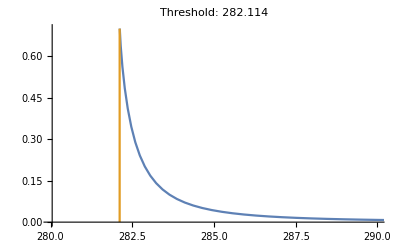

```mathematica
ListPlot[{Select[Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],0.7}}},PlotRange->{{280,290},All},Joined->True,PlotLabel->"Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

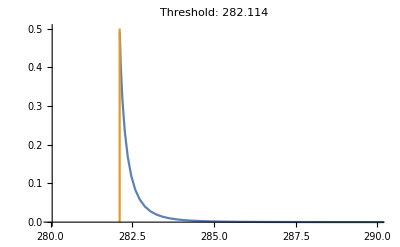

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],0.5}}},PlotRange->{{280,290},All},Joined->True,PlotLabel->"Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

### Debug

```mathematica
Block[{mQ=80,mq=60},m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[5];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[5];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
```

Wavefunction build complete.

```mathematica
Block[{ω1=0.907479105147823,ω2,Sen},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,Print["ω1=",ω1,"    ω2=",ω2];{Sen,MVG[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+MHG[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]]
```

ω1=0.907479    ω2=0.814958

{282.114,0.856536}

```mathematica
M1
M3
```

141.057

140.322

```mathematica
ω2fz[0.1][M1,M2,M3,M4]
```

9.11815

```mathematica
Sω1[ω1_]=Interpolation[Table[{ω1fz[z][M1,M2,M3,M4],√(S[z][M1,M2])},{z,0.00001,1,0.01}]][ω1];
```

```mathematica
FindMinimum[Sω1[ω1],{ω1,0.9}]
```

InterpolatingFunction::dmval: Input value {1.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{282.114,{ω1→0.906906}}

```mathematica
FindMinimum[Sω1[ω][M1,M2,M3,M4],{ω,0.5}]
```

{80435.2,{ω→0.873921}}

```mathematica
NMinimize[Sω1[ω][M1,M2,M3,M4],ω]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-4.01713×10^39,{ω→-4.95306×10^-36}}

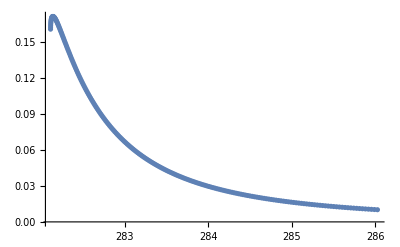

```mathematica
ListPlot[Table[{Sω1[x],Interpolation[list][x]},{x,0.7,0.9063125424888346,0.001}]](*This shows that with only MVG there can be a peak*)
```

```mathematica
FindRoot[ω1fz[z][M1,M2,M3,M4]==0.5,{z,0.5}]
```

{z→0.335635}

```mathematica
√(S[0.335635][M1,M2])
```

298.715

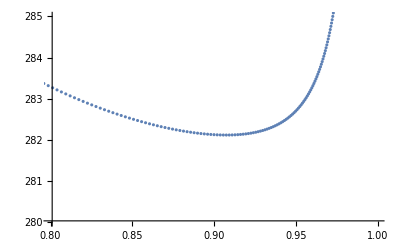

```mathematica
ListPlot[Table[{ω1fz[z][M1,M2,M3,M4],√(S[z][M1,M2])},{z,0.3,0.95,0.001}],PlotRange->{{0.8,0.9999},{280,285}}]
```

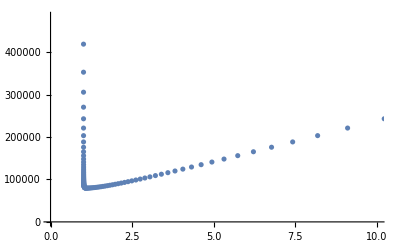

```mathematica
ListPlot[Table[{ω1fz[z][M1,M2,M3,M4],√(S[z][M1,M2])},{z,0.00001,1,0.01}]]
```

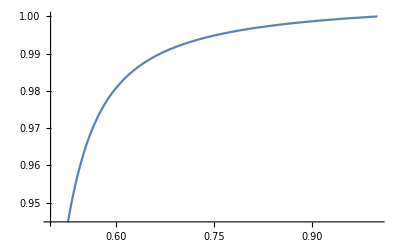

```mathematica
Plot[ω1fz[z][M1,M2,M3,M4],{z,0.5,1}]
```

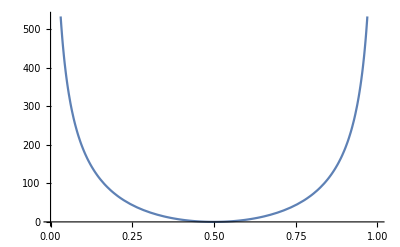

```mathematica
Plot[√(S[z][M1,M2])-M1-M2,{z,0,1}]
```

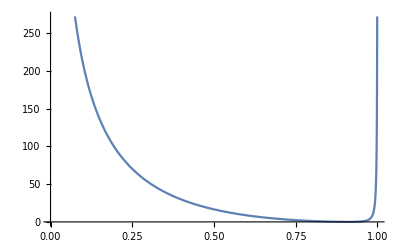

```mathematica
Plot[√(S[zfω[ω1][M1,M2,M3,M4]][M1,M2])-M1-M2,{ω1,0,1}]
```

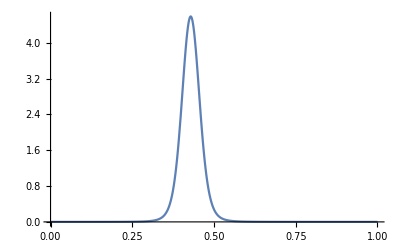

```mathematica
Plot[-ϕ3[1-y],{y,0,1},PlotRange->All]
```

```mathematica
g=1;
```

```mathematica
ω2n[0.5][M1,M2,M3,M4]
```

0.489712

```mathematica
Block[{ω1=0.4,ω2},ω2=ω2n[ω1][M1,M2,M3,M4];4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(y ω2-x(1+ω2-ω1)-ω1)^2 ϕ1[x]ϕ2[(y ω2)/ω1]ϕ3[ω1-ω2+(1-ω1+ω2)x]ϕ4[y],{x,0,1},{y,0,1}]]//AbsoluteTiming
```

{82.5583,0.00115006}

```mathematica
Block[{ω1=0.4,ω2},ω2=ω2n[ω1][M1,M2,M3,M4];4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(y ω2-x(1+ω2-ω1))^2 ϕ1[x]ϕ2[(y ω2)/ω1]ϕ3[ω1-ω2+x(1+ω2-ω1)]ϕ4[y],{x,0,1},{y,0,1},Method->"LocalAdaptive"]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.19947,0.503909}. NIntegrate obtained 3.70352×10^-7 and 5.01609×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.19947,0.503913}. NIntegrate obtained 2.21383×10^-7 and 1.4234×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.19947,0.503917}. NIntegrate obtained 1.1664×10^-6 and 2.72411×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
Block[{ω1=0.4,ω2},ω2=ω2n[ω1][M1,M2,M3,M4];4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(y ω2-x(1+ω2-ω1))^2 ϕ1[x]ϕ2[(y ω2)/ω1]ϕ3[ω1-ω2+x(1+ω2-ω1)]ϕ4[y],{x,0,1},{y,0,1},Method->"AdaptiveMonteCarlo"]]//AbsoluteTiming
```

$Aborted

```mathematica
Block[{ω1=0.49},MVG[ω1,ω2n[ω1][M1,M2,M3,M4]][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.000293161

```mathematica
Block[{ω1=0.55},MVG[ω1,ω2n[ω1][M1,M2,M3,M4]][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.000637646